#### Code:

```mathematica
(*Compute neighbors cells*)
NextCells[cells_List,adds_:{{1,0},{0,1},{-1,0},{0,-1}}]:=Complement[Union[Catenate[Outer[Plus,cells,adds,1]]],cells]
NextCellsMoore[cells_List] := NextCells[cells,Tuples[{-1,0,1},2]]
```

```mathematica
(*Check *)
TotalisticPruneQ[{rn_,offsets_},state_,newpos_]:=With[{
rulevec=Reverse[IntegerDigits[rn,2, Length[offsets]]]
},rulevec[[Total[Boole[MemberQ[state,newpos+#]&/@offsets]]]]==1]
```

```mathematica
NextAllowed[cells_List, rule_Integer] := Select[NextCellsMoore[cells],TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},cells,#]&]
```

```mathematica
RunAggSim[rule_Integer, initial_List] :=Module[{
binpath = FileNameJoin[{NotebookDirectory[],"chooser","bin","vis.exe"}]
},
Parametrize[str_] := StringJoin["\"",ToString@str,"\""];
Run @ StringRiffle[{binpath, Parametrize@rule, Parametrize@initial}," "]
]
```

```mathematica
PlotCells[cells_,opts:OptionsPattern[]]:=ArrayPlot[SparseArray[Thread[cells-Min[cells]+1->1],{Max[cells]-Min[cells]+1,Max[cells]-Min[cells]+1}],opts]
```

```mathematica
PlotCells[cells_,n_Integer,opts:OptionsPattern[]]:=ArrayPlot[SparseArray[Thread[cells+Ceiling[n/2]->1],{n,n}],opts]
```

```mathematica
PlotCellsEvent[cells_List,rule_Integer, opts:OptionsPattern[]] := EventHandler[PlotCells[cells,opts],{"MouseClicked":>RunAggSim[rule // Echo,cells]}]
```

```mathematica
TimedEchoProcedure[proc_,timeFunc_:Timing] := With[{output = timeFunc[proc[]]},Echo[First@output,"Execution time"];Last@output]
AbsoluteTimedEchoProcedure[proc_] := TimedEchoProcedure[proc,AbsoluteTiming]
```

```mathematica
AbsoluteTimedEchoProcedure[ParallelTable[Labeled[PlotCells[#,ImageSize->30,Mesh->True]&/@Last@HaltFind[rn, {{0,0},{1,1}},7],rn],{rn,Select[Range@255,MinNeigh[#]==2&]}]&]
```

Execution time  3.81099

{{}2,{}6,{}10,{}14,{-Graphics-}18,{}22,{-Graphics-}26,{}30,{}34,{}38,{}42,{}46,{-Graphics-}50,{}54,{-Graphics-}58,{}62,{}66,{}70,{}74,{}78,{-Graphics-}82,{}86,{-Graphics-}90,{}94,{}98,{}102,{}106,{}110,{-Graphics-}114,{}118,{-Graphics-}122,{}126,{}130,{}134,{}138,{}142,{-Graphics-}146,{}150,{-Graphics-}154,{}158,{}162,{}166,{}170,{}174,{-Graphics-}178,{}182,{-Graphics-}186,{}190,{}194,{}198,{}202,{}206,{-Graphics-}210,{}214,{-Graphics-}218,{}222,{}226,{}230,{}234,{}238,{-Graphics-}242,{}246,{-Graphics-}250,{}254}

```mathematica
AbsoluteTiming[ParallelTable[Labeled[PlotCells[#,ImageSize->30,Mesh->True]&/@Last@HaltFind[rn, {{0,0},{1,1}},7],rn],{rn,Select[Range@255,MinNeigh[#]==2&]}]]
```

{3.71199,{{}2,{}6,{}10,{}14,{-Graphics-}18,{}22,{-Graphics-}26,{}30,{}34,{}38,{}42,{}46,{-Graphics-}50,{}54,{-Graphics-}58,{}62,{}66,{}70,{}74,{}78,{-Graphics-}82,{}86,{-Graphics-}90,{}94,{}98,{}102,{}106,{}110,{-Graphics-}114,{}118,{-Graphics-}122,{}126,{}130,{}134,{}138,{}142,{-Graphics-}146,{}150,{-Graphics-}154,{}158,{}162,{}166,{}170,{}174,{-Graphics-}178,{}182,{-Graphics-}186,{}190,{}194,{}198,{}202,{}206,{-Graphics-}210,{}214,{-Graphics-}218,{}222,{}226,{}230,{}234,{}238,{-Graphics-}242,{}246,{-Graphics-}250,{}254}}

### Introduction

Aggregation systems are like cellular automata with a twist: once cells are set - i.e. aggregated - they remain set. The deterministic nature of standard CA is here replaced by a (standardly random) choice of what cell to add to the system, from a list of eligible cells according to the system rule.
We focus our study on totalistic rules - rules that inform if a cell is eligible based on the total number of neighbor cells active, instead of specific configurations around it.
Neighborhood  can be von Neumann (2^4  rules) or Moore(2^8  rules). Even though Moore is our main focus.
Here is an example of a Totalistic Moore aggregation system evolution, with rule 18 (10010). This system expands to cells with 2 or 5 active neighbors.
,,,,,,

Depending on the cells selected... (...halt)
Since we have, potentially, many ways to expand the system, is natural to ponder:

When is possible to make the system halt?

When is possible to make it grow “forever”?

### Simulation

We implement a simulation software to explore any set of rules, initial conditions, with both manual and random selection of aggregated cells.
The simulation was developed with Love2D, using the Lua language. Executable file was generated and integrated to the notebook available in the attachments. In desktop, clicking a cells plot will trigger the simulation.
(insert images)

### Multiway graphs

Since many choices can be made, is natural to consider the multiway graph representation of these systems.

(TODO: base graphs, depth, execution time)

```mathematica
Manipulate[NestGraph[Function[s,Union[Append[s,#]]&/@NextCells[s]],{{{0,0}}},n], {n,0,10, 1}]
```

```mathematica
Manipulate[Graph[NestGraph[Function[s,Union[Append[s,#]]&/@NextCells[s]],{{{0,0}}},n]], {n,0,10, 1}]
```

TotalisticManipulate

```mathematica
(* Revisit MOORE here! *)
TotalisticGraph[n_: 1, rule_: 242, initial_: {{0,0}}, usePlotCells_: False] := With[{
g = NestGraph[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], Union[Append[s,#]],Nothing]&/@NextCellsMoore[s]],{initial},n]
},
Graph[g,VertexLabels->(#->If[usePlotCells,PlotCells[#,ImageSize->15,Mesh->True],""]&/@VertexList[g]),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
]
TotalisticManipulate[rule_: 242, initial_: {{0,0}}, usePlotCells_: False] := Manipulate[
TotalisticGraph[n, rule, initial, usePlotCells],{n,0,10,1}]
```

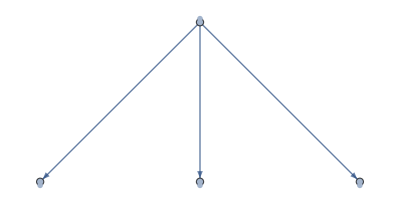

```mathematica
TotalisticGraph[1, 242, {{0,0},{1,1},{1,0},{1,-1},{2,-1}}, True]
```

```mathematica
TotalisticManipulate[242, {{0,0},{1,1},{1,0},{1,-1},{2,-1}}, True]
```

#### Introducing canonicalization (for translation): (convert list of cells to list of cells distanced from minimum coordinates among cells)

```mathematica
CellCanonicalize[state_]:=With[{m=Min/@Transpose[state]},#-m&/@state]
```

```mathematica
CellCanonicalize[{{0,0},{1,-2},{1,-1},{1,0},{1,1},{2,-1}}]
```

{{0,2},{1,0},{1,1},{1,2},{1,3},{2,1}}

```mathematica
TotalisticCanonManipulate[rule_: 242, initial_: {{0,0}}, usePlotCells_: False] := Manipulate[
With[{
g = NestGraph[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], CellCanonicalize[Union[Append[s,#]]],Nothing]&/@NextCells[s]],{CellCanonicalize[initial]},n]
},
Graph[g,VertexLabels->(#->If[usePlotCells,PlotCells[#,ImageSize->15, Mesh->True],""]&/@VertexList[g]),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
],{n,0,10,1}]
```

```mathematica
TotalisticCanonManipulate[rule_:242, initial_:{{0, 0}}, usePlotCells_:False] := 
	Manipulate[
		With[{
		g = NestGraph[Function[s, (If[TotalisticPruneQ[{rule, Tuples[{-1, 0, 1}, 2]}, s, #1],
CellCanonicalize[Union[Append[s, #1]]], Nothing] & ) /@ NextCells[s]], 
	{CellCanonicalize[initial]}, n]}, 
    Graph[g, VertexLabels -> (#1 -> If[usePlotCells, PlotCells[#1, ImageSize -> 15, Mesh -> True],
          ""] & ) /@ VertexList[g], GraphLayout -> "LayeredDigraphEmbedding", 
     AspectRatio -> 1/2]], {n, 0, 10, 1}]
```

```mathematica
TotalisticCanonManipulate[242, {{0,0},{1,-1}}, True]
```

```mathematica
TotalisticCanonManipulate[242, {{0,0},{-1,1},{0,1},{1,1}}, True]
```

#### Now with rotational canonicalization

```mathematica
CellCanonicalizeRotations[cells_]:=Module[{dim,mins,positive,array,canonarray},dim=Max[#]-Min[#]+1&/@Transpose[cells];
mins=Min/@Transpose[cells];
positive=#-mins+1&/@cells;
array=ReplacePart[ConstantArray[0,dim],positive->1];
canonarray=First[Sort[ResourceFunction["ArrayRotations"][ResourceFunction["ArrayCrop"][array]]]];
Position[canonarray,1]-1]
```

```mathematica
TotalisticFullCanonGraph[n_, rule_: 242, initial_: {{0,0}}, usePlotCells_: False, moore_: True] := With[{
g = NestGraph[Function[s,If[TotalisticPruneQ[{rule,Tuples[{-1,0,1},2]},s,#], CellCanonicalizeRotations[Union[Append[s,#]]],Nothing]&/@If[moore,NextCellsMoore[s],NextCells[s]]],{CellCanonicalizeRotations[initial]},n]
},
Graph[g,VertexLabels->(#->If[usePlotCells,PlotCells[#,ImageSize->15, Mesh->True],""]&/@VertexList[g]),GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/2]
]
```

```mathematica
TotalisticFullCanonManipulate[rule_: 242, initial_: {{0,0}}, usePlotCells_: False, moore_: True] := Manipulate[
TotalisticFullCanonGraph[n, rule, initial, usePlotCells, moore],{n,0,10,1}]
```

```mathematica
TotalisticCanonManipulate[1, {{0,0}}, True]
```

```mathematica
TotalisticFullCanonManipulate[242, {{0,0},{1,1}}, True]
```

### Halting states computation

#### Halt find

```mathematica
(* Computes list of states generated from 1 given state - list of cells *)
NextStates[rule_Integer, state_List] :=With[{neigh = Tuples[{-1,0,1},2]},If[TotalisticPruneQ[{rule,neigh},state,#],CellCanonicalizeRotations@Union@Append[state,#],Nothing]&/@NextCells[state,neigh]]
```

```mathematica
(* Computes list of all (flattened) states generated from list of states *)
NextStatesList[rule_Integer, states_List] := Union@Flatten[NextStates[rule, #]& /@ states,1]
```

```mathematica
HaltFindRaw[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3]:= NestWhile[NextStatesList[rule, #]&, {CellCanonicalizeRotations@initial}, True&, 1, maxn]
```

#### Halt find with halt states information

```mathematica
(*Compute/find minimum/first halting state*)
NextStatesListWithInfo[rule_Integer, states_List] := {Union@Flatten[#,1],states[[Flatten@Position[#,{}]]]}&@(NextStates[rule, #]& /@ states)
HaltFind[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3]:= NestWhile[NextStatesListWithInfo[rule, First[#]]&, {{CellCanonicalizeRotations@initial},{}}, Last[#]=={}&, 1, maxn]
```

```mathematica
(*Parallelized test*)
ParallelNextStatesListWithInfo[rule_Integer, states_List] := {Union@Flatten[#,1],states[[Flatten@Position[#,{}]]]}&@ParallelMap[NextStates[rule, #]& ,states]
ParallelHaltFind[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3]:= NestWhile[ParallelNextStatesListWithInfo[rule, First[#]]&, {{CellCanonicalizeRotations@initial},{}}, Last[#]=={}&, 1, maxn]
```

```mathematica
(*Compute all halting states*)
NextStatesListWithInfoAll[rule_Integer, data_List] := With[{states = First@data},{Union@Flatten[#,1],Join[Last@data,states[[Flatten@Position[#,{}]]]]}&@(NextStates[rule, #]& /@ states)]
HaltFindAll[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3] := Nest[NextStatesListWithInfoAll[rule, #]&, {{CellCanonicalizeRotations@initial},{}}, maxn]
```

```mathematica
(*Parallelized compute all halting states*)
ParallelNextStatesListWithInfoAll[rule_Integer, data_List] := With[{states = First@data},{Union@Flatten[#,1],Join[Last@data,states[[Flatten@Position[#,{}]]]]}&@ParallelMap[NextStates[rule, #]& ,states]]
ParallelHaltFindAll[rule_Integer: 242, initial_: {{0,0},{1,1}}, maxn_Integer: 3] := Nest[NextStatesListWithInfoAll[rule, #]&, {{CellCanonicalizeRotations@initial},{}}, maxn]
```

```mathematica
MinNeigh[rule_Integer]:=FirstPosition[Reverse@IntegerDigits[rule,2,8],1]//First
```

```mathematica
PlotBinaryGroups[method_,bit_Integer,initial_List,maxn_Integer] := (ParallelTable[Labeled[PlotCells[#,ImageSize->30,Mesh->True]&/@Last@method[rn, initial,maxn],rn],{rn,Select[Range@255,MinNeigh[#]==bit&]}]&) // AbsoluteTimedEchoProcedure
```

```mathematica
PlotBinaryGroupsHalt[bit_Integer,initial_List,maxn_Integer, allHalts_: False] := PlotBinaryGroups[If[allHalts,HaltFindAll,HaltFind],bit,initial,maxn]
```

```mathematica
PlotBinaryGroupsParallelHalt[bit_Integer,initial_List,maxn_Integer, allHalts_: False] := PlotBinaryGroups[If[allHalts,ParallelHaltFindAll,ParallelHaltFind],bit,initial,maxn]
```

```mathematica
PlotBinaryGroupsParallelHalt[2,{{0,0},{1,1}},11, True]
```

{{-Graphics-}2,{}6,{-Graphics-}10,{}14,{-Graphics-,-Graphics-,-Graphics-}18,{}22,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}26,{}30,{}34,{}38,{}42,{}46,{-Graphics-,-Graphics-}50,{}54,{-Graphics-,-Graphics-,-Graphics-}58,{}62,{-Graphics-}66,{}70,{-Graphics-}74,{}78,{-Graphics-,-Graphics-,-Graphics-}82,{}86,{-Graphics-,-Graphics-,-Graphics-,-Graphics-}90,{}94,{}98,{}102,{}106,{}110,{-Graphics-,-Graphics-}114,{}118,{-Graphics-,-Graphics-,-Graphics-}122,{}126,{-Graphics-}130,{}134,{-Graphics-}138,{}142,{-Graphics-,-Graphics-}146,{}150,{-Graphics-,-Graphics-,-Graphics-}154,{}158,{}162,{}166,{}170,{}174,{-Graphics-}178,{}182,{-Graphics-,-Graphics-}186,{}190,{-Graphics-}194,{}198,{-Graphics-}202,{}206,{-Graphics-,-Graphics-}210,{}214,{-Graphics-,-Graphics-,-Graphics-}218,{}222,{}226,{}230,{}234,{}238,{-Graphics-}242,{}246,{-Graphics-,-Graphics-}250,{}254}

```mathematica
PlotBinaryGroupsHalt[2,{{0,0},{1,1}},10, False]
```

Execution time  84.6227

{{}2,{}6,{}10,{}14,{-Graphics-}18,{}22,{-Graphics-}26,{}30,{}34,{}38,{}42,{}46,{-Graphics-}50,{}54,{-Graphics-}58,{}62,{}66,{}70,{}74,{}78,{-Graphics-}82,{}86,{-Graphics-}90,{}94,{}98,{}102,{}106,{}110,{-Graphics-}114,{}118,{-Graphics-}122,{}126,{}130,{}134,{}138,{}142,{-Graphics-}146,{}150,{-Graphics-}154,{}158,{}162,{}166,{}170,{}174,{-Graphics-}178,{}182,{-Graphics-}186,{}190,{}194,{}198,{}202,{}206,{-Graphics-}210,{}214,{-Graphics-}218,{}222,{}226,{}230,{}234,{}238,{-Graphics-}242,{}246,{-Graphics-}250,{}254}

```mathematica
(*PlotBinaryGroupsParallelHalt[2,{{0,0},{1,1}},8, False];*)
(Table[Labeled[PlotCells[#,ImageSize->30,Mesh->True]&/@Last@ParallelHaltFind[r, {{0,0},{1,1}},10],rn],{rn,Select[Range@255,MinNeigh[#]==2&]}]&) // AbsoluteTimedEchoProcedure;
```

2

6

10

14

18

22

26

30

34

38

42

46

50

54

58

62

66

70

74

78

82

86

90

94

98

102

106

110

114

118

122

126

130

134

138

142

146

150

154

158

162

166

170

174

178

182

186

190

194

198

202

206

210

214

218

222

226

230

234

238

242

246

250

254

Execution time  163.293

```mathematica
PlotBinaryGroupsOnlyHalt[bit_Integer,initial_List,maxn_Integer] := Select[PlotBinaryGroupsHalt[bit,initial,maxn],#[[1]]=!={}&]
```

```mathematica
TimedProcedurePlot[proc_] := TimedEchoProcedure[proc] //
If[Length[#]==0,"No halt found",PlotCells[First[#],ImageSize->100,Mesh->True]]&
TimedHaltFindPlot[rule_Integer, initial_List, maxn_Integer] := TimedProcedurePlot [Last@HaltFind[rule, initial, maxn]&]
```

```mathematica
(*Parallel case*)
TimedParallelHaltFindPlot[rule_Integer, initial_List, maxn_Integer] := TimedProcedurePlot[Last@ParallelHaltFind[rule, initial, maxn]&]
```

```mathematica
TimedHaltFindPlot[2,First@MinimalInitials@2,11]
TimedParallelHaltFindPlot[2,First@MinimalInitials@2,11]
```

Execution time  1.20313

-Graphics-

Execution time  0.171875

-Graphics-

## Exploring bit groups

#### Definition: k-Bit rule: a rule where the bit k is the lower bit set, i.e., system admit cells with exactly k neighbors and possibly more (but not less). is the set of k-bit rules.

```mathematica
bitGroups = Function[bit,Select[Range@255,MinNeigh[#]==bit&]] /@ Range@8 ;
formattedData = Transpose @{Range@Length@bitGroups,StringJoin["(#",ToString@Length@#,"): ",StringRiffle[ToString/@#,","]]&/@ bitGroups};
Print[Grid[Prepend[formattedData,{"Bit","Bit Rules Set"}],Frame->All,Alignment->Left]];
```

Bit | Bit Rules Set
1 | (#128): 1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199,201,203,205,207,209,211,213,215,217,219,221,223,225,227,229,231,233,235,237,239,241,243,245,247,249,251,253,255
2 | (#64): 2,6,10,14,18,22,26,30,34,38,42,46,50,54,58,62,66,70,74,78,82,86,90,94,98,102,106,110,114,118,122,126,130,134,138,142,146,150,154,158,162,166,170,174,178,182,186,190,194,198,202,206,210,214,218,222,226,230,234,238,242,246,250,254
3 | (#32): 4,12,20,28,36,44,52,60,68,76,84,92,100,108,116,124,132,140,148,156,164,172,180,188,196,204,212,220,228,236,244,252
4 | (#16): 8,24,40,56,72,88,104,120,136,152,168,184,200,216,232,248
5 | (#8): 16,48,80,112,144,176,208,240
6 | (#4): 32,96,160,224
7 | (#2): 64,192
8 | (#1): 128

#### Remarks: 1) 2) If all bits set in a rule are set in a rule , the multiway-system graph of is contained in . After all, a system with can do all choices can. We say contains 3) The lower rule in a k-Bit group is contained by all other rules in the same group. It should then be the easiest to compute. 4) Analogously, the higher rule contains all others, and then should be harder to compute.

### 4 connectivity:

#### 1-Bit rules never halt

Proof: Let s be any given state (collection of cells). There will be a set of cells with higher horizontal coordinate. Let p be the coordinates of the cell from this set with higher vertical coordinate. The cells at positions p+{-1,1} and p+{1,1} will be unset, so the cell at p+{0,1} will have exactly one neighbor. So the system can grow with it.

#### Non 1-Bit rules always halt

Proof: Let s be any given state (collection of cells). Let r be any rectangle that contains all cells from s. A cell outside r will have, at most, 1 neighbors cell inside rUs. It is then impossible to add a cell from outside, and so the system will halt eventually
-Graphics-

### 8 connectivity:

#### 1-Bit rules never halt.

Proof: Let s be any given state (collection of cells). There will be a set of cells with higher horizontal coordinate. Let p be the coordinates of the cell from this set with higher vertical coordinate. The cell at position p+{1,1} will have exactly one neighbor. So the system can grow with it.
-Graphics-

#### ()-Bit rules always halt.

-Graphics-
Proof: Let s be any given state (collection of cells). Let r be any rectangle that contains all cells from s. A cell outside r will have, at most, 3 neighbors cell inside rUs. It is then impossible to add a cell from outside, and so the system will halt eventually

#### Left with 2-Bit and 3-Bit

## Analysis and Simulations

PlotBinaryGroupsHalt gives us the list of halting states found for given rule, initial cells and maximum depth.
A k-Bit rule requires a minimum of k initial cells in order to not halt instantly (trivially). MinimalInitials provides the set of minimal initial cells for a given rule.

```mathematica
MinimalInitials[bit_Integer] := Tuples[Range[bit],2] // Subsets[#,{bit}]& // (CellCanonicalizeRotations/@#)& // Union
PlotMinimalInitials[bit_Integer]:=PlotCells[#,ImageSize->30,Mesh->True]&/@ MinimalInitials[bit]
ShowSteps[cells_List,start_Integer] := PlotCells[#,ImageSize->100,Mesh->True]&/@Table[Take[#,i],{i,start,Length[#]}]&@CellCanonicalize@cells
```

### 1-Bit

As we already know, we cannot halt with 1-Bit rules:

```mathematica
PlotBinaryGroupsHalt[1,{{0,0}},8]
```

{{}1,{}3,{}5,{}7,{}9,{}11,{}13,{}15,{}17,{}19,{}21,{}23,{}25,{}27,{}29,{}31,{}33,{}35,{}37,{}39,{}41,{}43,{}45,{}47,{}49,{}51,{}53,{}55,{}57,{}59,{}61,{}63,{}65,{}67,{}69,{}71,{}73,{}75,{}77,{}79,{}81,{}83,{}85,{}87,{}89,{}91,{}93,{}95,{}97,{}99,{}101,{}103,{}105,{}107,{}109,{}111,{}113,{}115,{}117,{}119,{}121,{}123,{}125,{}127,{}129,{}131,{}133,{}135,{}137,{}139,{}141,{}143,{}145,{}147,{}149,{}151,{}153,{}155,{}157,{}159,{}161,{}163,{}165,{}167,{}169,{}171,{}173,{}175,{}177,{}179,{}181,{}183,{}185,{}187,{}189,{}191,{}193,{}195,{}197,{}199,{}201,{}203,{}205,{}207,{}209,{}211,{}213,{}215,{}217,{}219,{}221,{}223,{}225,{}227,{}229,{}231,{}233,{}235,{}237,{}239,{}241,{}243,{}245,{}247,{}249,{}251,{}253,{}255}

### 2-Bit

```mathematica
Echo [PlotMinimalInitials[2],"Initial states: "];
```

Initial states:   {-Graphics-,-Graphics-}

#### Initial redundancy

Is easy to see that both initial states result in same configurations, regardless of the subsequent bits:

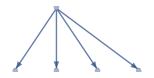
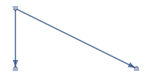

```mathematica
TotalisticGraph[1,2,#,True]& /@ MinimalInitials[2] // Row[#,Spacer[18]]&
```

#### Halting and performance

For this rule, branching factor is substantially high and the maximum we can compute of the multiway graph is 9 iterations.
Computing only states (no edges) with HaltFind is considerably lighter on memory and faster.
Running 11 steps in the simplest rule gives us a halting configuration:

```mathematica
TimedHaltFindPlot[6,First@MinimalInitials@2,9]
```

Last::argt: Last called with 0 arguments; 1 or 2 arguments are expected.

Execution time  0.

No halt found

```mathematica
TimedHaltFindPlot[First@bitGroups[[2]],First@MinimalInitials@2,11]
```

Execution time  1.42188

-Graphics-

Rules with more branching can get quite more expensive to run. The most complicated rule (254) is more than 10x slower:

```mathematica
TimedHaltFindPlot[254,First@MinimalInitials@2,11]
```

Execution time  36.6719

No halt found

```mathematica
Timing[HaltFind[6,First@MinimalInitials@2,11]//Last];
Echo[First@%,"Execution time"];
If[Length[Last@%%]==0,"No halt found",PlotCells[%%[[2,1]],ImageSize->100,Mesh->True]]
```

Execution time  26.3906

No halt found

```mathematica
(*Parallel test*)
Timing[ParallelHaltFind[254,First@MinimalInitials@2,12]//Last];
Echo[First@%,"Execution time"];
If[Length[Last@%%]==0,"No halt found",PlotCells[%%[[2,1]],ImageSize->100,Mesh->True]]
```

Execution time  12.9375

No halt found

Let’s see the minimum halting states we can find, up to 11 steps, for each 2-Bit rules:

```mathematica
PlotBinaryGroupsHalt[2,{{0,0},{1,1}},11]
```

{{-Graphics-}2,{}6,{-Graphics-}10,{}14,{-Graphics-}18,{}22,{-Graphics-}26,{}30,{}34,{}38,{}42,{}46,{-Graphics-}50,{}54,{-Graphics-}58,{}62,{-Graphics-}66,{}70,{-Graphics-}74,{}78,{-Graphics-}82,{}86,{-Graphics-}90,{}94,{}98,{}102,{}106,{}110,{-Graphics-}114,{}118,{-Graphics-}122,{}126,{-Graphics-}130,{}134,{-Graphics-}138,{}142,{-Graphics-}146,{}150,{-Graphics-}154,{}158,{}162,{}166,{}170,{}174,{-Graphics-}178,{}182,{-Graphics-}186,{}190,{-Graphics-}194,{}198,{-Graphics-}202,{}206,{-Graphics-}210,{}214,{-Graphics-}218,{}222,{}226,{}230,{}234,{}238,{-Graphics-}242,{}246,{-Graphics-}250,{}254}

#### Subcase analysis:

Rule 2 is the lesser rule of 2-bit group, so its halting state is a state reachable by every other rule in the group. Even though all other rules can reach this state, they do not necessarily get stuck on it. The condition to halt is easy to see when we observe the boundary of the system. The 2 neighbors cells in the “side holes” require bit 6 to expand, while all others require either bits 1 or 3.
This means that having bits 3 and 6 unset makes this state a halting state. This means a quarter of the 64 cells in the 2-bit group reach this halting state:

```mathematica
FromDigits[Reverse@#,2]&/@Select[Tuples[{0,1},8],And[#[[1]]==0,#[[2]]==1, #[[3]]==0, #[[6]]==0] &] // Sort
```

{2,10,18,26,66,74,82,90,130,138,146,154,194,202,210,218}

Interestingly, for many of them, we can find a halt state with even less steps than rule 2:

#### Subcase analysis:

Is easy to see that a required condition for this state to be halting is that the rule cannot have bit 3. This is all we need to get stuck in this state (since every cell has 3 or less neighbors), but we need a little bit more to be able to get in this state. Analyzing the tree we can see how we got there:

```mathematica
ShowSteps[{{1,3},{2,4},{2,3},{2,2}, {3,2},{3,1},{4,2},{3,3}},6,2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The last block required bit 5 to be set. All others required only bit 2.
But what if we consider adding this last block earlier?

```mathematica
ShowSteps[{{1,3},{2,4},{2,3},{2,2}, {3,2},{3,3},{3,1},{4,2}},6,2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The last block required bit 3 to be set, and that is a contradiction.
Conclusion: this halting state happens when bit 3 is unset and bit 5 is set. These rules are:

```mathematica
FromDigits[Reverse@#,2]&/@Select[Tuples[{0,1},8],And[#[[1]]==0,#[[2]]==1, #[[3]]==0, #[[5]]==1] &] // Sort
```

{18,26,50,58,82,90,114,122,146,154,178,186,210,218,242,250}

Exactly the ones seem in the group halt plot, as expected.

#### Special subcase analysis:

This state was found manually and requires 19 steps, using only bit 2 insertions.
To be halting though needs bits 3, 4, 6 unset. Having bit 7 set lets the system grow 2 steps adding the cells in the interior, and then also halts.

```mathematica
FromDigits[Reverse@#,2]&/@Select[Tuples[{0,1},8],And[#[[1]]==0,#[[2]]==1, #[[3]]==0, #[[4]]==0, #[[6]]==0] &] // Sort
```

{2,18,66,82,130,146,194,210}

These rules are a subset of the rules that reach the lesser rule halting state

### 3-Bit

```mathematica
Echo [PlotMinimalInitials[3],"Initial states: "];
```

Initial states:   {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ReducedMinimal3 = MinimalInitials[3][[{3,5,6,7,9,10}]];
Echo [PlotCells[#,ImageSize->30,Mesh->True]&/@ ReducedMinimal3,"Reduced initial states: "];
```

Reduced initial states:   {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

(reduction explained in the following section)

#### Initial redundancy

##### Initials and are equivalent after 1 step

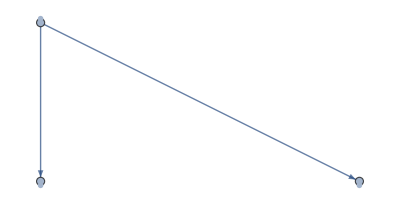
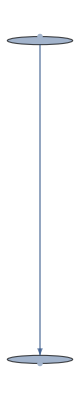

```mathematica
TotalisticGraph[1,4,#,True]& /@ MinimalInitials[3][[{1,3}]]
```

■ Not only that,  is different after 1 step, but after 2 steps it is also equivalent to ,

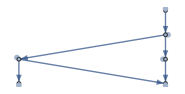
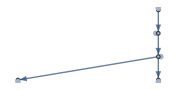

```mathematica
TotalisticFullCanonGraph[3,4,#,True]& /@ MinimalInitials[3][[{3,4}]]
```

■ Apart from that,  is quite trivial, since it halts after 1 step.
■   is an unique combination of 3 cells in a 3x3 grid, but is still invalid as it provides no eligible cell to be inserted.
Note that all this observations does not depend on the subsequent bits of the rule, since for these rules, first 2 steps has only 3-bit eligible cells.

#### Halting and performance

3-Bit rules has a substantially lower branching factor. We can compute several more steps than 2-Bit rules (around 10 more steps).
First we begin looking for halting with the lesser (simplest) 3-bit rule, rule 4:

```mathematica
TimedHaltFindPlot[First@bitGroups[[3]],First@MinimalInitials@3,15]
```

Execution time  0.53125

-Graphics-

And running with the more complicated 3-bit rule, rule 252, we cannot find halting:

```mathematica
TimedHaltFindPlot[Last@bitGroups[[3]],First@MinimalInitials@3,21]
```

Execution time  47.4688

No halt found

Let’s see the minimum halting states we can find, up to 11 steps, for each 3-Bit rules:

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[1]],20]
```

{{-Graphics-}4,{}12,{-Graphics-}20,{}28,{-Graphics-}36,{}44,{-Graphics-}52,{}60,{-Graphics-}68,{}76,{-Graphics-}84,{}92,{-Graphics-}100,{}108,{-Graphics-}116,{}124,{-Graphics-}132,{}140,{-Graphics-}148,{}156,{-Graphics-}164,{}172,{-Graphics-}180,{}188,{-Graphics-}196,{}204,{-Graphics-}212,{}220,{-Graphics-}228,{}236,{-Graphics-}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[5]],17]
```

{{-Graphics-}4,{}12,{-Graphics-}20,{}28,{-Graphics-}36,{}44,{-Graphics-}52,{}60,{-Graphics-}68,{}76,{-Graphics-}84,{}92,{-Graphics-}100,{}108,{-Graphics-}116,{}124,{-Graphics-}132,{}140,{-Graphics-}148,{}156,{-Graphics-}164,{}172,{-Graphics-}180,{}188,{-Graphics-}196,{}204,{-Graphics-}212,{}220,{-Graphics-}228,{}236,{-Graphics-}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[6]],17]
```

{{}4,{}12,{}20,{}28,{}36,{}44,{}52,{}60,{}68,{}76,{}84,{}92,{}100,{}108,{}116,{}124,{}132,{}140,{}148,{}156,{}164,{}172,{}180,{}188,{}196,{}204,{}212,{}220,{}228,{}236,{}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[7]],17]
```

{{-Graphics-,-Graphics-}4,{}12,{-Graphics-,-Graphics-,-Graphics-}20,{}28,{-Graphics-,-Graphics-}36,{}44,{-Graphics-,-Graphics-,-Graphics-}52,{}60,{-Graphics-,-Graphics-}68,{}76,{-Graphics-,-Graphics-,-Graphics-}84,{}92,{-Graphics-,-Graphics-}100,{}108,{-Graphics-,-Graphics-,-Graphics-}116,{}124,{-Graphics-,-Graphics-}132,{}140,{-Graphics-,-Graphics-,-Graphics-}148,{}156,{-Graphics-,-Graphics-}164,{}172,{-Graphics-,-Graphics-,-Graphics-}180,{}188,{-Graphics-,-Graphics-}196,{}204,{-Graphics-,-Graphics-,-Graphics-}212,{}220,{-Graphics-,-Graphics-}228,{}236,{-Graphics-,-Graphics-,-Graphics-}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[9]],17]
```

{{}4,{}12,{}20,{}28,{}36,{}44,{}52,{}60,{}68,{}76,{}84,{}92,{}100,{}108,{}116,{}124,{}132,{}140,{}148,{}156,{}164,{}172,{}180,{}188,{}196,{}204,{}212,{}220,{}228,{}236,{}244,{}252}

```mathematica
PlotBinaryGroupsHalt[3,MinimalInitials[3][[10]],17]
```

{{-Graphics-,-Graphics-}4,{}12,{-Graphics-,-Graphics-,-Graphics-}20,{}28,{-Graphics-,-Graphics-}36,{}44,{-Graphics-,-Graphics-,-Graphics-}52,{}60,{-Graphics-,-Graphics-}68,{}76,{-Graphics-,-Graphics-,-Graphics-}84,{}92,{-Graphics-,-Graphics-}100,{}108,{-Graphics-,-Graphics-,-Graphics-}116,{}124,{-Graphics-,-Graphics-}132,{}140,{-Graphics-,-Graphics-,-Graphics-}148,{}156,{-Graphics-,-Graphics-}164,{}172,{-Graphics-,-Graphics-,-Graphics-}180,{}188,{-Graphics-,-Graphics-}196,{}204,{-Graphics-,-Graphics-,-Graphics-}212,{}220,{-Graphics-,-Graphics-}228,{}236,{-Graphics-,-Graphics-,-Graphics-}244,{}252}

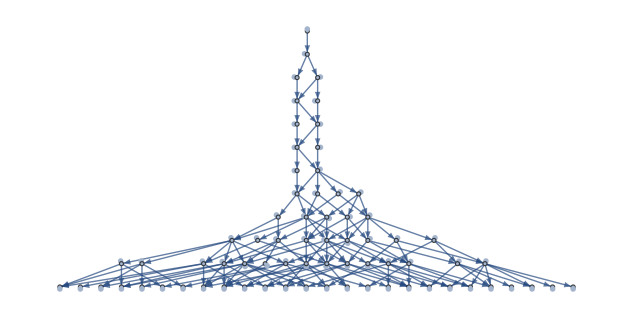

```mathematica
TotalisticFullCanonGraph[11,4,{{0,0},{1,1},{0,2}}, True]
```

```mathematica
TotalisticFullCanonManipulate[76,{{0,0},{0,1},{1,2}}, True]
```

```mathematica
PlotCells[{{0,0},{1,1},{1,0},{1,-1}},ImageSize->30,Mesh->True]
```

-Graphics-

## Misc...

Discuss parallelization of separate routines X routines in sequence and parallelization of routine internals

```mathematica
(*2 sequentiall operations to SOW in halting states (Reap around everything)*)
If[halt_test, Sow[state]];state
```

state

```mathematica
HaltLeadTestState = {{0,0},{-1,1},{-2,2},{0,1},{-1,2},{1,1},{0,2}};
HaltTestState = Append[HaltLeadTestState, {-1,3}];
PlotCells[#,ImageSize->30,Mesh->True]&/@ {HaltLeadTestState,HaltTestState}
```

{-Graphics-,-Graphics-}